```mathematica
(*Match the gamma mmoments*)
(*First moment*)
```

```mathematica
Clear["Global`*"]
appgammalap[s_]:=Exp[(2 π (1/α)^(2/β) λ Gamma[2/β] PolyLog[2/β,-s])/β];
appgammamoment1=-Limit[appgammalap'[s],s->0,Direction->"FromAbove",Assumptions->{α>0,β>0,λ>0}];
appgammamoment2=Simplify[Limit[appgammalap''[s],s->0,Direction->"FromAbove"],Assumptions->{α>0,β>0,λ>0}];

plotυ=FullSimplify[appgammamoment1^2/(appgammamoment2-appgammamoment1^2)]

plotγ=FullSimplify[(appgammamoment2-appgammamoment1^2)/(appgammamoment1)]
```

(4^(1/β) π α^(-2/β) λ Gamma[2/β])/β

2^((-2+β)/β)

0.125

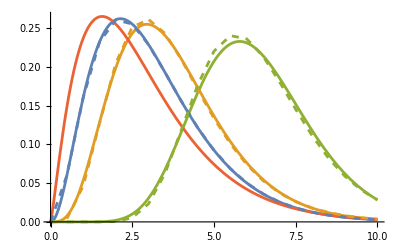

```mathematica
max=10.;
λ=1;
α=1.;

Show[Plot[{β=2;PDF[GammaDistribution[plotυ,plotγ]][t],β=1.5;PDF[GammaDistribution[plotυ,plotγ]][t],β=1;PDF[GammaDistribution[plotυ,plotγ]][t],β=3;PDF[GammaDistribution[plotυ,plotγ]][t]},{t,0,max}],ListLinePlot[{table1,table2,table3},PlotStyle->Dashed]]
```

```mathematica
β=2.;table1=ParallelTable[{t,InverseLaplaceTransform[appgammalap[s],s,t]},{t,0,max,0.5}];β=1.5;table2=ParallelTable[{t,InverseLaplaceTransform[appgammalap[s],s,t]},{t,0,max,0.5}];β=1;table3=ParallelTable[{t,InverseLaplaceTransform[appgammalap[s],s,t]},{t,0,max,0.5}];
β=0.5;table4=ParallelTable[{t,InverseLaplaceTransform[appgammalap[s],s,t]},{t,0,max,0.5}];
```

```mathematica
Table[t,{t,1,10,0.1}]
```

```mathematica
(*Beta:*)

Clear["Global`*"]

λ=1;

NNfun[t_]:=(2 ⅇ^(-π λ (-Log[t]/α)^(2/β)) π λ (-Log[t]/α)^(-1+2/β))/(t α β);

appbetamom1[α_,β_]:=NIntegrate[(2 ⅇ^(-π λ (-Log[t]/α)^(2/β)) π λ (-Log[t]/α)^(-1+2/β))/(t α β)*t, {t,0,1}];
appbetamom2[α_,β_]:=
NIntegrate[(2 ⅇ^(-π λ (-Log[t]/α)^(2/β)) π λ (-Log[t]/α)^(-1+2/β))/(t α β)*t^2, {t,0,1}];

μ[α_,β_]:=(appbetamom1[α,β]*(1-appbetamom1[α,β])/(appbetamom2[α,β]-appbetamom1[α,β]^2)-1)*appbetamom1[α,β];
σ[α_,β_]:=(appbetamom1[α,β]*(1-appbetamom1[α,β])/(appbetamom2[α,β]-appbetamom1[α,β]^2)-1)*(1-appbetamom1[α,β]);
```

```mathematica
(*Plot[μ[0.7,β],{β,0.7,2}]
Plot[σ[0.7,β],{β,0.7,2}]
Plot[μ[α,0.7],{α,0.7,2}]
Plot[σ[α,0.7],{α,0.7,2}]*)
```

General::munfl: Exp[-785.603] is too small to represent as a normalized machine number; precision may be lost.

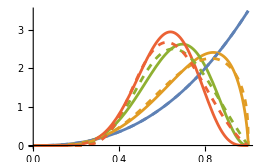

```mathematica
max=1.;
α=0.9;
Show[Plot[{β=2;PDF[BetaDistribution[μ[α,β],σ[α,β]]][t],β=1.5;PDF[BetaDistribution[μ[α,β],σ[α,β]]][t],β=1;PDF[BetaDistribution[μ[α,β],σ[α,β]]][t],β=0.8;PDF[BetaDistribution[μ[α,β],σ[α,β]]][t]},{t,0,max}],Plot[{β=2;NNfun[t],β=1.5;NNfun[t],β=1;NNfun[t],β=0.9;NNfun[t]},{t,0,max},PlotStyle->Dashed]]
```